```mathematica
(*constants*)
ACC = 10000;
HWCap = 2.4*10^-3 ;(*nF*)
BIOCap =0.24; (*nF*)
vShift = 1200;
vAlpha = 10;
(*calibration*)(*from calibtic.cpp*)
El[V_]:=1.02*V-8.58;
gl[x_]:=5.52*10^-5*x^2+0.24*x+0.89; (*10^-5 instead of 10^-10 in M.O.Schwartz thesis*)
Vsyntc[x_]:=-3.94*x^2+37*x+1382;
Vt[V_]:= 0.998*V-3.55;
Ipl[x_]:=1/(0.025*x-0.0004);
Igladapt[x_]:=4.93*10^-5*x^2+0.26*x-0.66;
Iradapt[x_]:=1/(-4.4*10^-6*x^2+0.00032*x-0.0005);
Ifire[x_]:=-0.14*x^2+45*x+54.75;
Irexp[x_]:=9.2386*x^2+66.3847*x-94.2541;
Vexp[V_]:=0.3720*V + 100.2902(*93.15+0.64*V;*);
```

```mathematica
(*scaling*)
scaleV[V_] := vAlpha * V + vShift;
scaleConductance[x_]:=x* ACC * HWCap/BIOCap;
scaleCurrent[x_] := x * vAlpha * ACC * HWCap/BIOCap;
scaleDeltaT[x_] := x * 10;
scaleTau[x_]:=x/ACC * 1000;
```

```mathematica
(*transformations*)
transmempot[V_]:=El[scaleV[V]];
transthresh[V_]:=Vt[scaleV[V]];
transtcmem[x_]:=gl[scaleConductance[x]];
transtcsyn[x_] :=Vsyntc[scaleTau[x]];
transdeltat[x_] := Irexp[scaleDeltaT[x]];
transvexp[V_]:=Vexp[scaleV[V]];
transtcref[x_] := Ipl[scaleTau[x]];
transtcadapt[x_] := Iradapt[scaleTau[x]];
transadapt[x_] := Igladapt[scaleConductance[x]];
transb[x_] := Ifire[scaleCurrent[x]];
(*plots*)
```

```mathematica
(*LIF membrane dynamics*)
```

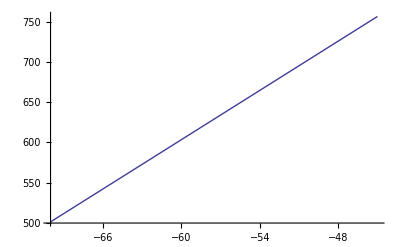

```mathematica
Plot[transmempot[V],{V,-70,-45}] (*also valid for E_syn, V_reset*)
```

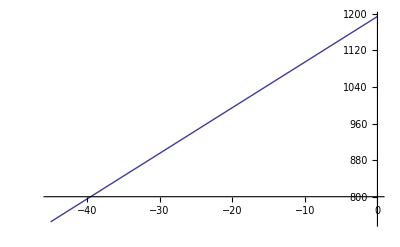

```mathematica
Plot[transthresh[V],{V,-45,0}]
```

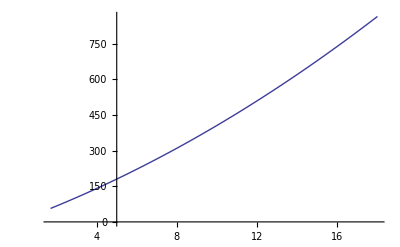

```mathematica
Plot[transtcmem[x], {x,1.7,18}]
```

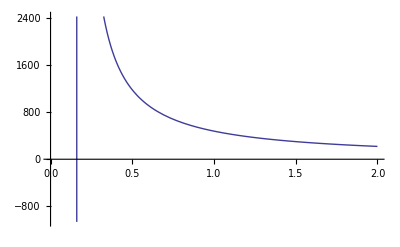

```mathematica
Plot[transtcref[x], {x,0,2}](*diverges... but ok for biological ref > 0.4ms *)
```

```mathematica
(*Adaptation term*)
```

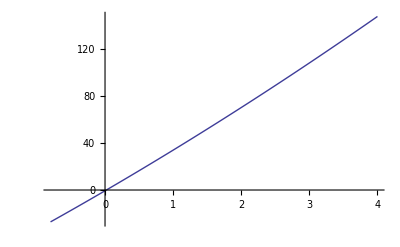

```mathematica
Plot[transadapt[x],{x,-0.8,4}]
```

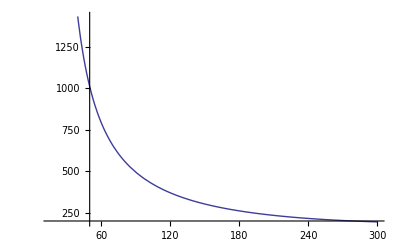

```mathematica
Plot[transtcadapt[x],{x,16,300}]
```

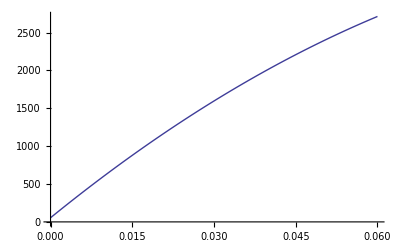

```mathematica
Plot[transb[x],{x,0,0.06}]
```

```mathematica
(*Exponential term*)
```

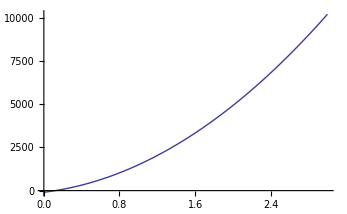

```mathematica
Plot[transdeltat[x],{x,0, 3}]
```

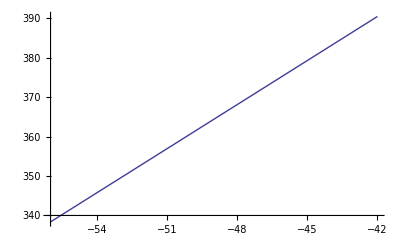

```mathematica
Plot[transvexp[V],{V,-56,-42}]
```

```mathematica
(*synaptic input*)
```

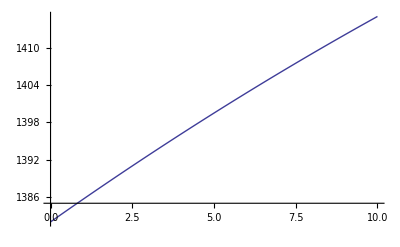

```mathematica
Plot[transtcsyn[x], {x,0,10}]
```

```mathematica
mvoltdac[x_] := x * 1023 / 1800; 
currdac[x_] := x * 1023 / 2500;
```

```mathematica
(*test data for calibtic.cpp *)
```

```mathematica
currdac[transtcref[1.0035]]
```

194.049

```mathematica
currdac[transadapt[2.3872]]
```

26.2775

```mathematica
currdac[transtcmem[18]] (* needs a conductance as input in contrast to calibtic which gets a time*)
```

250.323

```mathematica
mvoltdac[transmempot[5.2301]]
```

721.083

```mathematica
mvoltdac[transmempot[-80.2931]]
```

225.305

```mathematica
currdac[transdeltat[1.54]]
```

1276.33

```mathematica
currdac[transb[0.1001]]
```

1291.62

```mathematica
mvoltdac[transtcsyn[10.0001]]
```

804.226

```mathematica
mvoltdac[transthresh[0.0103]]
```

678.677

```mathematica
currdac[transtcadapt[100.0500]]
```

180.969

```mathematica
mvoltdac[transmempot[-60.23109]]
```

341.604

```mathematica
mvoltdac[transvexp[-50.2010]]
```

204.567